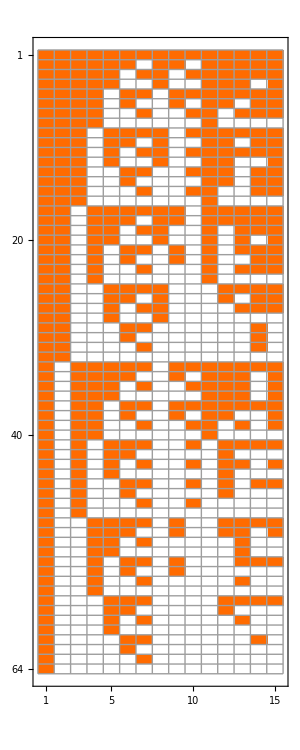
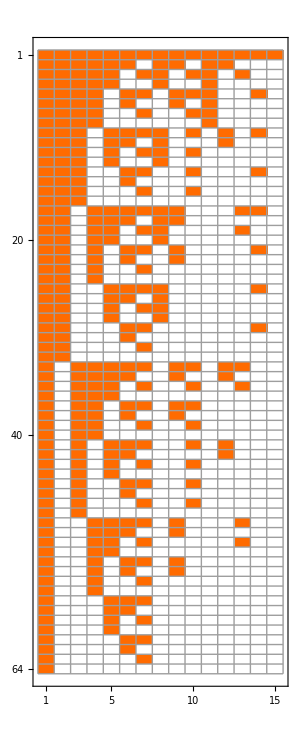

```mathematica
Row[{
MatrixPlot[Sort[Table[VectorOne[BaseCoeff4[k,"E"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&],Mesh->All,ImageSize->300],
MatrixPlot[Sort[Table[BaseCoeff4[k,"C"],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&],Mesh->All,ImageSize->300]
},ImageSize->1200]
```

```mathematica
Sort[Table[Total[BaseCoeff4[k,"C"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]]//Tally
```

{{1,1},{2,6},{3,12},{4,7},{5,16},{7,15},{10,6},{15,1}}

```mathematica
VectorSize[vect_]:=Total[Map[If[#==0,0,1]&,vect]]
```

```mathematica
Vector1[vect_]:=Map[If[#==0,0,1]&,vect]
```

```mathematica
Rest[Total[Table[Vector1[BaseCoeff4[k,"G"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]]]//Total
```

170

```mathematica
Total[Table[Vector1[BaseCoeff4[k,"C"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]]//Total
```

337

```mathematica
Total[Table[Vector1[BaseCoeff4[k,"E"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}]]//Total
```

470

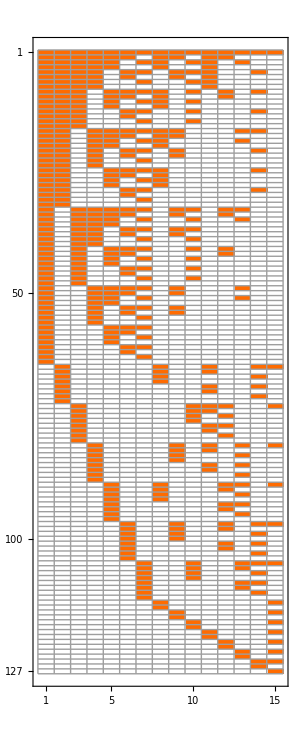

```mathematica
MatrixPlot[Sort[Table[BaseCoeff4[k,"C"],{k,Keys[allGraphs4]}],FromDigits[#1,2]>FromDigits[#2,2]&],Mesh->All,ImageSize->300]
```

```mathematica
With[
{base="C"},
Map[Style[#,Red,20]&,((Sort[Table[VectorOne[BaseCoeff4[k,base]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&]//Total))]*(Map[allGraphs4[#,"graph"]&, Bases4[base,"AtomKeys"]])
]
```

{-Graphics- 64,-Graphics- 32,-Graphics- 32,-Graphics- 32,-Graphics- 32,-Graphics- 32,-Graphics- 32,-Graphics- 16,-Graphics- 16,-Graphics- 16,-Graphics- 8,-Graphics- 8,-Graphics- 8,-Graphics- 8,-Graphics- 1}

```mathematica
With[
{base="G"},
Map[Style[#,Red,20]&,((Sort[Table[VectorOne[BaseCoeff4[k,base]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&]//Total))]*(Map[allGraphs4[#,"graph"]&, Bases4[base,"AtomKeys"]])
]
```

{-Graphics- 38,-Graphics- 16,-Graphics- 16,-Graphics- 16,-Graphics- 16,-Graphics- 16,-Graphics- 16,-Graphics- 15,-Graphics- 15,-Graphics- 15,-Graphics- 7,-Graphics- 7,-Graphics- 7,-Graphics- 7,-Graphics- 1}

```mathematica
VectorOne[vect_]:=Map[If[#==0,0,1]&,vect]
```

```mathematica
((Sort[Table[VectorOne[BaseCoeff4[k,"E"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&]//Total)/64)*(Map[allGraphs4[#,"graph"]&, Bases4["E","AtomKeys"]])
```

{-Graphics-,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/4,(-Graphics-)/4,(-Graphics-)/4,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(-Graphics-)/2,(19 -Graphics-)/32}

```mathematica
Sort[Table[VectorOne[BaseCoeff4[k,"E"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&]==Sort[Table[VectorOne[BaseCoeff4[k,"C"]],{k,Select[Keys[allGraphs4],VertexCount[allGraphs4[#,"graph"]]==4&]}],FromDigits[#1,2]>FromDigits[#2,2]&]
```

False